# e+e-→μ +μ-

### PROCESS:

```mathematica
CKM = IndexDelta;
Neglect[MU] = Neglect[MU2] = 0;
Neglect[MM] = Neglect[MM2] = 0;
process ={-F[2, {1}], F[2, {1}]} -> {-F[2, {2}], F[2, {2}]} ;

SetOptions[InsertFields,  Model -> "SM",InsertionLevel->{Particles}, Restrictions -> NoLightFHCoupling];
(*SetOptions[CreateFeynAmp, GaugeRules -> {GaugeXi[Z] -> ZGAUGE, GaugeXi[A] -> AGAUGE,
 GaugeXi[W] -> WGAUGE} ];*)
```

## SM: Feynman rules and diagrams

```mathematica
CHARGESZl={QZLl->-1,QZUl->2/3,QZDl->-1/3,I3D->-1/2,I3L->-1/2,I3N->1/2,I3U->1/2};
CHARGESZr={QZLr->-1,QZUr->2/3,QZDr->-1/3};
CHARGESphl={QLl->-1,QUl->2/3,QDl->-1/3};
CHARGESphr={QLr->-1,QUr->2/3,QDr->-1/3};
MASSES={MM->0,MM2->0,ME->0,ME2->0,S+T+U->0}
```

{MM→0,MM2→0,ME→0,ME2→0,S+T+U→0}

```mathematica
(*GENERALIZZAZIONE CARICHE/ISOSPIN PER CASO SM*)
coupling[x_]:=Module[{Mcouplin,chargenuZ,chargelepZ,chargeupZ,chargedownZ,n,m,chargenup,chargelep,chargedown,chargeup},

Mcouplin=M$CouplingMatrices;
(*____________________________  Z COUPLING  ______________________________*)
(*neutrino*)
chargenuZ[(lhs:C[_. F[1,{__}],_. F[1,{__}],_. V[2]])==rhs_]:=
lhs==(rhs/.{
	dZZZ1-> 2 I3N dZZZ1,
	1/(2 CW SW)->I3N/(CW SW),
	EL IndexDelta[j1_,j2_]->2*I3N*EL IndexDelta[j1,j2]
	

});
chargenuZ[other_]=other;
Mcouplin=chargenuZ/@Mcouplin;

(*lepton*)
chargelepZ[(lhs:C[_. F[2,{__}],_. F[2,{__}],_. V[2]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{-(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(2 CW SW)->I3L*(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(CW SW),
			SW/CW->-QZLl SW/CW,
			(-1/2+SW^2)->(I3L-QZLl*SW^2),
			dZAZ1->- QLl dZAZ1 (*CT misto gamma Z*)
			},
		rhsR/.{
		SW/CW->-QZLr SW/CW,
		dZAZ1->- QLr dZAZ1 (*CT misto gamma Z*)
		}
});
chargelepZ[other_]=other;
Mcouplin=chargelepZ/@Mcouplin;

(*q up*)
chargeupZ[(lhs:C[_. F[3,{__}],_. F[3,{__}],_. V[2]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(2 CW SW)->I3U*(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(CW SW),
			(1/2-2/3SW^2)->(I3U-QZUl*SW^2),
			
			dZAZ1->3/2 QUl dZAZ1,(*CT misto gamma Z: − δ [g1,g2] QU δZ(γZ)/2*)
			-2/3->-QZUl},
		rhsR/.{
			-dZAZ1 /3->-QUr*dZAZ1 /2, (*CT misto gamma Z*)
			-1/3 I*EL->-QZUr/2 I*EL,
			-2/3*I->-QZUr*I,
			-2/3->-QZUr,
			-SW /(3*CW)->-QZUr*SW /(2*CW)}
});
chargeupZ[other_]=other;
Mcouplin=chargeupZ/@Mcouplin;

(*q down*)
chargedownZ[(lhs:C[_. F[4,{__}],_. F[4,{__}],_. V[2]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{
			-(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(2 CW SW)->I3D*(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(CW SW),
			(-1/2+1/3 SW^2)->(I3D-QZDl*SW^2),
			dZAZ1->-3 QDl dZAZ1, (*CT misto gamma Z*)
			1/3->-QZDl},
			
		rhsR/.{
			dZZZ1->- 3 QZDr*dZZZ1 ,
			dZAZ1->- 3 QDr*dZAZ1 ,(*CT misto gamma Z*)
			1/3 I*EL->-QZDr I*EL,
			1/3*I->-QZDr*I,
			1/3->-QZDr,
			SW /(3*CW)->-QZDr*SW /(CW)}
});
chargedownZ[other_]=other;
Mcouplin=chargedownZ/@Mcouplin;

(*____________________________  GAMMA COUPLING  ___________________________*)
(*neutrino*)
chargenup[(lhs:C[_. F[1,{__}],_. F[1,{__}],_. V[1]])==rhs_]:=
lhs==(rhs/.{
		EL IndexDelta[j1_,j2_]->2*I3N*EL IndexDelta[j1,j2]
});
chargenup[other_]=other;
Mcouplin=chargenup/@Mcouplin;
(*lepton*)
chargelep[(lhs:C[_. F[2,{__}],_. F[2,{__}],_. V[1]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(-1/2+SW^2)->(I3L-QZLl*SW^2)/-QLl,(*CT misto gamma Z*)
			I->-QLl*I,
			1/2*I->-1/2 QLl*I
},
			
		rhsR/.{dZZA1->- QZLr dZZA1/-QLr,(*CT misto gamma Z*)
		I->-QLr*I,
			1/2*I->-1/2 QLr*I
		}
});
chargelep[other_]=other;
Mcouplin=chargelep/@Mcouplin;

(*q up*)
chargeup[(lhs:C[_. F[3,{__}],_. F[3,{__}],_. V[1]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(1/2-2/3SW^2)->(I3U-QZUl*SW^2),(*CT misto gamma Z*)
			-2/3->-QUl,
			-2/3*I->-QUl*I},
			
		rhsR/.{dZZA1->3/2 QZUr dZZA1,(*CT misto gamma Z*)
		-2/3->-QUr,
		-2/3*I->-QUr*I}
});
chargeup[other_]=other;
Mcouplin=chargeup/@Mcouplin;

(*q down*)
chargedown[(lhs:C[_. F[4,{__}],_. F[4,{__}],_. V[1]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(-1/2+1/3 SW^2)->(I3D-QZDl*SW^2),(*CT misto gamma Z*)
			1/3->-QDl,
			1/3*I->-QDl*I
			},
							
	rhsR/.{ dZZA1->-3 QZDr dZZA1,(*CT misto gamma Z*)
			1/3->-QDr,
			1/3*I->-QDr*I}
});
chargedown[other_]=other;
Mcouplin=chargedown/@Mcouplin;

Mcouplin
];
```

```mathematica
InitializeModel["SM",
ModelEdit :>{
M$ClassesDescription=M$ClassesDescription//.{(-Charge)->QL Charge,(2/3Charge)->QU Charge,(-1/3Charge)->QD Charge},
M$CouplingMatrices=coupling[M$CouplingMatrices]}

];
```

loading generic model file /home/arianna/Documenti/FeynArts-3.11/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /home/arianna/Documenti/FeynArts-3.11/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counterterms of order 1

> 6 counterterms of order 2

classes model {SM} initialized

## Feynman Diagrams

## Tree Level

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

Restoring 18 field point(s)

in total: 2 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

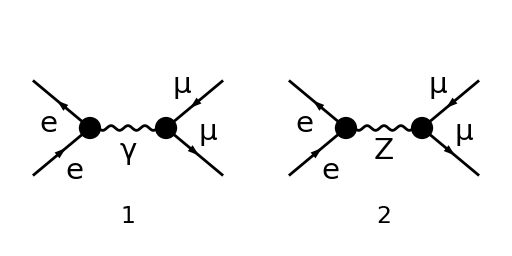

FeynArtsGraphics[][([1] | [2])]

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

in total: 2 Particles amplitudes

```mathematica
tops = CreateTopologies[0, 2 -> 2];
ins = InsertFields[tops, process];
Paint[ins,ColumnsXRows->{2,1},Numbering->Simple,
SheetHeader->None,ImageSize->{512,256}]
born1=CreateFeynAmp[ins];
```

## Amplitude

```mathematica
(*set variabili semplificate*)
mzg=Times[MZ,Power[ZGAUGE,Rational[1,2]]];
mwg=Times[MW,Power[WGAUGE,Rational[1,2]]];
P1=FourMomentum[Incoming,1];
P2=FourMomentum[Incoming,2];
Q1=FourMomentum[Internal,1];
K1=FourMomentum[Outgoing,1];
K2=FourMomentum[Outgoing,2];
```

METTERE MANUALMENTE: 1 per fotone e 2 per z per born diagram

```mathematica
(*funzione per semplificare propagatori*)
numer[x__ PropagatorDenominator[p_,MZ] PropagatorDenominator[p_,mzg]]:=numer[x/(MZ^2-mzg^2)(PropagatorDenominator[p,MZ]-PropagatorDenominator[p,mzg])];
numerw[x__ PropagatorDenominator[p_,MW] PropagatorDenominator[p_,mwg]]:=numerw[x/(MW^2-mwg^2)(PropagatorDenominator[p,MW]-PropagatorDenominator[p,mwg])];
```

```mathematica
(*BORN*)
born=Part[born1,{1}][[1,3]]//.{Index[Lorentz, 1]->Index[Lorentz, bn1],Index[Lorentz, 2]->Index[Lorentz, bn2]}//.MASSES;
bornchains=DeleteCases[Cases[born,_FermionChain,Infinity],_IndexDelta,Infinity];
conjbornchains=CONJ/@Reverse[bornchains,{2}] 
(*colour matrix*)
colourborn=Union[Cases[born,_SumOver|_IndexDelta,Infinity]]
(*born propagators*)
bornpropag=DeleteCases[born, _SumOver | _FermionChain,Infinity]/.FeynAmpDenominator->Times;
bornpropag2=Collect[numer/@%/.numer->Sequence//Simplify,
PropagatorDenominator[x_,mzg],Simplify]//.FourVector[a__]:>Distribute[FourVector[a]]/.FourVector->SP /.MetricTensor->SP/.PropagatorDenominator[a_,b_]->1/(a^2-b^2)
```

{CONJ[v̄[p2,0].(-ⅈ EL QLl ga[Lorbn1].om_--ⅈ EL QLr ga[Lorbn1].om_+).u[p1,0]],CONJ[ū[k1,0].(-ⅈ EL QLl ga[Lorbn2].om_--ⅈ EL QLr ga[Lorbn2].om_+).v[k2,0]]}

{}

SP[Lorbn1,Lorbn2]/(k1+k2)^2

```mathematica
bornch=bornchains//.{Index[Lorentz, bn1]->Index[Lorentz, 1],Index[Lorentz, bn2]->Index[Lorentz, 2]}
```

{v̄[p1,0].(-ⅈ EL QLl ga[Lor1].om_--ⅈ EL QLr ga[Lor1].om_+).u[p2,0],ū[k2,0].(-ⅈ EL QLl ga[Lor2].om_--ⅈ EL QLr ga[Lor2].om_+).v[k1,0]}

```mathematica
(*propagatore totale:*)
```

```mathematica
b1=bornpropag2//.{Index[Lorentz, bn1]->Index[Lorentz, 1],Index[Lorentz, bn2]->Index[Lorentz, 2]}
btot=bornpropag2 b1
```

SP[Lor1,Lor2]/(k1+k2)^2

(SP[Lor1,Lor2] SP[Lorbn1,Lorbn2])/(k1+k2)^4

#### Trace

```mathematica
trg[s___,MM,u___]:=MM trg[s,u];
trg[z___,-G5]:=-trg[z,G5];
trg[a_,b_,G5]:=0;
trg[a_,b_,c_,d_,G5]:=-4 I LC myEps[a,b,c,d];
trg[x___,G5,G5,y___]:=trg[x,y];
trg[x__,G5]:=0/;OddQ[Length[{x}]];
trg[q___,G5,y__]:=trg[q,y,G5](-1)^(Length[{y}]);
trg[a_,b_]:=4 SP[a,b];
trg[w__]:=0/;OddQ[Length[{w}]] && FreeQ[{w},G5];

(*TRACE*)
trg[x__]:=Module[{temp,temp1,temp2,i,temp3},

temp={x};
temp1=Delete[temp,1];
temp2=Table[Delete[temp1,i],{i,1,Length[temp1]}];
temp3=Sum[SP[temp[[1]],temp1[[i]]](-1)^(i+1)*Apply[trg,temp2[[i]]],{i,1,Length[temp2]}];
temp3=Expand[temp3];

temp3
];
```

```mathematica
(*funzioni prodotto scalare e levicivita*)
SetAttributes[SP,Orderless];
SP/:SP[Index[u__],Index[v__]] SP[p_,Index[u__]] := SP[p,Index[v]];
SP/:SP[a_,Index[mu__]]^2 := SP[a,a];
SP/:SP[a_,Index[mu__]] SP[b_,Index[mu__]] := SP[a,b];
SP/:SP[Index[mu__],Index[mu__]] = d;
SP/:SP[Index[mu__],Index[nu__]]^2 = d;
SP/:SP[-b_,a_]:=-SP[b,a];
(*levicivita product. 4 indices (d->4)*)
myEps/:myEps[a__]^2:=-Expand@Det@Outer[SP,{a},{a}];
myEps/:myEps[a__] myEps[b__]:=-Expand@Det@Outer[SP,{a},{b}];
```

```mathematica
move2[a___,ChiralityProjector[pm_],dm:MM,b___]:=move2[a,dm,ChiralityProjector[pm],b];
move2[a___,ChiralityProjector[pm_],dm:_DiracMatrix|_DiracSlash,b___]:=move2[a,dm,ChiralityProjector[-pm],b];
move2[a___,ChiralityProjector[x_],ChiralityProjector[y_],b___]:=0/;x≠y;
move2[a___,ChiralityProjector[x_],ChiralityProjector[y_],b___]:=move2[a,ChiralityProjector[x],b]/;x==y;
(*NOTA: ANTICOMMUTAZIONE IN D-DIMENSIONI *)
```

```mathematica
(*calcolo traccia*)
trace2[chargesi_,statoi_,chargesf_,statof_]:=Module[{tr1i,tr2i,tr3i,tr1f,tr2f,tr3f,tracciai,tracciaf,chii,chff,tracei,tracef},

(*trace:*)
traceff[x___, DiracSpinor[z_,w_], DiracSpinor[z_,w_],y___]:=traceff[x,(DiracSlash[z]+w),y];(* ...u(p)u_bar(p) ... -> ...p_slash... *)(*sost. stato intermedio*)
traceff[ DiracSpinor[z_,w_],x__,DiracSpinor[z_,w_]]:=traceff[(DiracSlash[z]+w),x];(* v_bar(p)...v(p) ->p_slash... *)(*sost. stato esterno*)

(*stato i*)
tr1i=Table[traceff[statoi[[i]]/.List->Sequence],{i,1,Length[statoi]}]//.traceff->move2;(*sposto proiettori in fondo*)
chii=Delete[chargesi,Position[tr1i,0,{1}]];(*cariche*)
tr2i=Map[Distribute,1/2 DeleteCases[tr1i,0,1]//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)},Infinity];(*sostituisco om+- con espressioni G5 esplicite*)
tr3i=DeleteCases[tr2i,1,{4}]//.move2->trg/.{DiracMatrix->Sequence,DiracSlash->Sequence}//Expand;(*espando e calcolo traccia*)
tracciai=tr3i/.{ SP[a_,b_]:>Distribute[SP[a,b]], myEps[a_,b__]:>Distribute[myEps[a,b]]}//Expand;

(*stato f*)
tr1f=Table[traceff[statof[[i]]/.List->Sequence],{i,1,Length[statof]}];
tr1f=Replace[Table[Distribute[tr1f[[i]]],{i,1,Length[tr1f]}],Plus->Sequence,{2},Heads->True]//.traceff->move2;
If[FreeQ[statf,MM,Infinity],
chff=Delete[chargesf,Position[tr1f,0,{1}]],
chff=chargesf];(*cariche*)
tr2f=Map[Distribute,1/2 DeleteCases[tr1f,0,1]//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)},{2}];
tr3f=DeleteCases[tr2f,1,{4}]//.move2->trg/.{DiracMatrix->Sequence,DiracSlash->Sequence}//Expand;
tracciaf=DeleteCases[tr3f/.{ SP[a_,b_]:>Distribute[SP[a,b]], myEps[a_,b__]:>Distribute[myEps[a,b]]},0]//Expand;

Print["stato i ",1/2 DeleteCases[tr1i,0,1]//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)},"\n stato f ",
1/2 DeleteCases[tr1f,0,1]//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)}];

tracei=Thread[List[chii,tracciai]];
tracef=Thread[List[chff,tracciaf]];

Return[{tracei,tracef}]

];
```

```mathematica
(*input->diag=loop diagram *)
fermiontrace[diag_]:=Module[{tborn1,tborn2,hb,hbc,tborn3i,tborn3ic,tborn3f,tborn3fc,fermionchain,sti,sti1,tbi,tbic,tbi2,tbi3,tbi3c,stf,stf1,tbf,tbfc,tbf2,tbf3,tbf3c},
(*****BORN*****)
tborn1=Table[Map[Distribute,conjbornchains,3][[i]],{i,1,2}];
tborn2=Apply[List,tborn1,{1}]/.CONJ->Sequence;
(*seleziono termini per calcolo traccia e cariche*)
hb=Table[Table[Cases[tborn2[[j,i]],_NonCommutative,Infinity],{i,1,Length[tborn2[[j]]]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence,{j,1,2}];
hbc=Table[Table[DeleteCases[tborn2[[j,i]],_NonCommutative,Infinity],{i,1,Length[tborn2[[j]]]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence,{j,1,2}];
(*STATO I*)
tborn3i=Flatten[Select[hb,MemberQ[#,DiracSpinor[-P1,_],Infinity]&],1];
tborn3ic=Flatten[Select[hbc,MemberQ[#,QZUl|QLl,Infinity]&],1];(*charges/coupling*)
(*STATO F*)
tborn3f=Flatten[Select[hb,MemberQ[#,DiracSpinor[-K1,_],Infinity]&],1];
tborn3fc=Flatten[Select[hbc,MemberQ[#,QZLl|QLl,Infinity]&],1];(*charges/coupling*)

(*****LOOP DIAGRAM*****)
(*trace closed fermion loop(if any)*)
tr=Cases[diag,_MatrixTrace,Infinity];
(*fermionchain without tr and with external particles masses->0*)
input=DeleteCases[diag,_MatrixTrace,Infinity]//.MASSES;
(*fermionchain part for trace computation*)
fermionchain=DeleteCases[Cases[input,_FermionChain,Infinity],_SUNT|_IndexDelta,Infinity];
(*select fermionchain, expand sums, split state i/f*)
tab1=Table[Distribute[fermionchain[[i]]],{i,1,2}];
(*STATO I*)
sti=Select[tab1,MemberQ[#,DiracSpinor[-P1,_],Infinity]&];(*select stato i*)
If[MemberQ[sti,Plus[FermionChain[__],_],Infinity],sti1=Flatten[Apply[List,sti,{1}],1],sti1=sti];(*suddivide in lista se ha piu elementi*)
(*seleziono termini per calcolo traccia e cariche*)
tbi=Table[Cases[sti1[[i]],_NonCommutative,Infinity],{i,1,Length[sti1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;
tbic=Table[DeleteCases[sti1[[i]],_NonCommutative,Infinity],{i,1,Length[sti1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;

tbi2=Table[move2@@tbi[[i]],{i,1,Length[tbi]}]//.move2->List;(*sposto proiettori in fondo a destra con anticommutazione*)
tbi3=DeleteCases[tbi2,0,1];
tbi3c=Delete[tbic,Position[tbi2,0,{1}]];(*semplificazione se ci sono dei termini nulli dove ho om- om+ *)
(*union diag*born*)
stati=Flatten[Table[{Join[tbi3[[i]],tborn3i[[1]]],Join[tbi3[[i]],tborn3i[[2]]]},{i,1,Length[tbi3]}],1];
chi=Flatten[Table[{Join[tbi3c[[i]],tborn3ic[[1]]],Join[tbi3c[[i]],tborn3ic[[2]]]},{i,1,Length[tbi3c]}],1]//.FermionChain->Times;

(*STATO F*)(*procedimento analogo a STATO I*)
stf=Select[tab1,MemberQ[#,DiracSpinor[K2,_],Infinity]&];
If[MemberQ[stf,Plus[FermionChain[__],_],Infinity],stf1=Flatten[Apply[List,stf,{1}],1],stf1=stf];
tbf=Table[Cases[stf1[[i]],_NonCommutative,Infinity],{i,1,Length[stf1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;
tbfc=Table[DeleteCases[stf1[[i]],_NonCommutative,Infinity],{i,1,Length[stf1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;
tbf2=Replace[Table[Distribute[tbf[[i]]//.List->f],{i,1,Length[tbf]}],Plus->Sequence,{2},Heads->True]//.f->move2;
tbf3=DeleteCases[tbf2,0,1]//.move2->List;
If[FreeQ[tbf2,MM,Infinity],
tbf3c=Delete[tbfc,Position[tbf2,0,{1}]],
tbf3c=tbfc];(*semplificazione se ci sono dei termini nulli dove ho om- om+ *)
statf=Flatten[Table[{Join[tbf3[[i]],tborn3f[[1]]],Join[tbf3[[i]],tborn3f[[2]]]},{i,1,Length[tbf3]}],1];
chf=Flatten[Table[{Join[tbf3c[[i]],tborn3fc[[1]]],Join[tbf3c[[i]],tborn3fc[[2]]]},{i,1,Length[tbf3c]}],1]//.FermionChain->Times;

prova1=trace2[chi,stati,chf,statf];

Return[{tr,prova1}](*closed fermion loop, trace*)
];
```

```mathematica
bornch//.CHARGESphl//.CHARGESphr//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)}
```

{v̄[p1,0].(ⅈ EL ga[Lor1].(1-G5)+ⅈ EL ga[Lor1].(1+G5)).u[p2,0],ū[k2,0].(ⅈ EL ga[Lor2].(1-G5)+ⅈ EL ga[Lor2].(1+G5)).v[k1,0]}

```mathematica
conjbornchains//.CHARGESphl//.CHARGESphr//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)}
```

{CONJ[v̄[p2,0].(ⅈ EL ga[Lorbn1].(1-G5)+ⅈ EL ga[Lorbn1].(1+G5)).u[p1,0]],CONJ[ū[k1,0].(ⅈ EL ga[Lorbn2].(1-G5)+ⅈ EL ga[Lorbn2].(1+G5)).v[k2,0]]}

```mathematica
boxt=fermiontrace[bornch]
```

stato i {1/2 move2[gs[-(p1)],ga[Lor1],gs[p2],ga[Lorbn1],1-G5],1/2 move2[gs[-(p1)],ga[Lor1],gs[p2],ga[Lorbn1],1+G5]}
 stato f {1/2 move2[gs[k2],ga[Lor2],gs[-(k1)],ga[Lorbn2],1-G5],1/2 move2[gs[k2],ga[Lor2],gs[-(k1)],ga[Lorbn2],1+G5]}

{{},{{{-4 Alfa π QLl^2,2 ⅈ LC myEps[-(p1),Lor1,p2,Lorbn1]-2 SP[p1,Lorbn1] SP[p2,Lor1]-2 SP[p1,Lor1] SP[p2,Lorbn1]+2 SP[p1,p2] SP[Lor1,Lorbn1]},{-4 Alfa π QLr^2,-2 ⅈ LC myEps[-(p1),Lor1,p2,Lorbn1]-2 SP[p1,Lorbn1] SP[p2,Lor1]-2 SP[p1,Lor1] SP[p2,Lorbn1]+2 SP[p1,p2] SP[Lor1,Lorbn1]}},{{-4 Alfa π QLl^2,2 ⅈ LC myEps[k2,Lor2,-(k1),Lorbn2]-2 SP[k1,Lorbn2] SP[k2,Lor2]-2 SP[k1,Lor2] SP[k2,Lorbn2]+2 SP[k1,k2] SP[Lor2,Lorbn2]},{-4 Alfa π QLr^2,-2 ⅈ LC myEps[k2,Lor2,-(k1),Lorbn2]-2 SP[k1,Lorbn2] SP[k2,Lor2]-2 SP[k1,Lor2] SP[k2,Lorbn2]+2 SP[k1,k2] SP[Lor2,Lorbn2]}}}}

```mathematica
(*suddivido lo stato i ed f (che hanno due termini ciascuno) in parte delle cariche e parte con myEps/senza myEps*)
```

```mathematica
(*Il fatto che però ci siano solo 3 impulsi indipendenti (per la conserv. p1+p2=k1+k2) rende i termini con myEps nulli perché non ci sono abbastanza quantità per saturare gli indici mantenendo l’antisimmetria.
quindi i prodotti sono solo fra termini con myEps e senza myEps ma non misti.*)
(*ho stato i con due termini (Q1i*i1,Q2i*i2) e stato f (Q1f*f1,Q2f*f2) a loro volta composti da parte con myEps e senza. faccio il prodotto. ho 4 termini STAT: STAT[1,1] STAT[1,2] STAT[2,1] STAT[2,2] *)
```

```mathematica
Table[{chargeI[i]=boxt[[2,1,i,1]],
ieps[i]={Select[boxt[[2,1,i,2]],MemberQ[#,_myEps,Infinity]&]},
ineps[i]={Select[boxt[[2,1,i,2]],FreeQ[#,_myEps,Infinity]&]}}
,{i,1,Length[boxt[[2,1]]]}];
Table[{chargeF[i]=boxt[[2,2,i,1]],
feps[i]={Select[boxt[[2,2,i,2]],MemberQ[#,_myEps,Infinity]&]},
fneps[i]={Select[boxt[[2,2,i,2]],FreeQ[#,_myEps,Infinity]&]}}
,{i,1,Length[boxt[[2,2]]]}];
```

```mathematica
(******************per caso MM ≠0 mettere ({j,1,4}) per MM=0 ({j,1,2}), anche per {l,1,4} piu in basso ****************************)
```

```mathematica
Table[{CHARGE[i,j]={chargeI[i] chargeF[j]},STAT[i,j]={ParallelMap[ieps[i]*#&,feps[j]]//Expand,ParallelMap[ineps[i]*#&,fneps[j]]}//.List->Plus//Expand},{i,1,2},{j,1,2}];
(*nota: se ho masse MM gli elementi con myEps rimangono nel calcolo (per poter fare il prodotto con stesso numero di el
fra parte con myeps e senza: ho infatti ieps[1] e [2] e feps da 1 a 4 ) *)
Table[STAT[i,j]=DeleteCases[STAT[i,j],_myEps,Infinity],{i,1,2},{j,1,2}]
```

{{-4 LC^2 SP[p1,Lorbn2] SP[p2,Lor2] SP[k1,Lorbn1] SP[k2,Lor1]+4 LC^2 SP[p1,Lor2] SP[p2,Lorbn2] SP[k1,Lorbn1] SP[k2,Lor1]+4 SP[p1,Lorbn1] SP[p2,Lor1] SP[k1,Lorbn2] SP[k2,Lor2]+4 SP[p1,Lor1] SP[p2,Lorbn1] SP[k1,Lorbn2] SP[k2,Lor2]+4 LC^2 SP[p1,Lorbn2] SP[p2,Lor2] SP[k1,Lor1] SP[k2,Lorbn1]-4 LC^2 SP[p1,Lor2] SP[p2,Lorbn2] SP[k1,Lor1] SP[k2,Lorbn1]+4 SP[p1,Lorbn1] SP[p2,Lor1] SP[k1,Lor2] SP[k2,Lorbn2]+4 SP[p1,Lor1] SP[p2,Lorbn1] SP[k1,Lor2] SP[k2,Lorbn2]+4 LC^2 SP[p1,Lorbn2] SP[p2,k2] SP[k1,Lorbn1] SP[Lor1,Lor2]-4 LC^2 SP[p1,k2] SP[p2,Lorbn2] SP[k1,Lorbn1] SP[Lor1,Lor2]-4 LC^2 SP[p1,Lorbn2] SP[p2,k1] SP[k2,Lorbn1] SP[Lor1,Lor2]+4 LC^2 SP[p1,k1] SP[p2,Lorbn2] SP[k2,Lorbn1] SP[Lor1,Lor2]-4 SP[p1,p2] SP[k1,Lorbn2] SP[k2,Lor2] SP[Lor1,Lorbn1]-4 SP[p1,p2] SP[k1,Lor2] SP[k2,Lorbn2] SP[Lor1,Lorbn1]-4 LC^2 SP[p1,Lor2] SP[p2,k2] SP[k1,Lorbn1] SP[Lor1,Lorbn2]+4 LC^2 SP[p1,k2] SP[p2,Lor2] SP[k1,Lorbn1] SP[Lor1,Lorbn2]+4 LC^2 SP[p1,Lor2] SP[p2,k1] SP[k2,Lorbn1] SP[Lor1,Lorbn2]-4 LC^2 SP[p1,k1] SP[p2,Lor2] SP[k2,Lorbn1] SP[Lor1,Lorbn2]-4 LC^2 SP[p1,Lorbn2] SP[p2,k2] SP[k1,Lor1] SP[Lor2,Lorbn1]+4 LC^2 SP[p1,k2] SP[p2,Lorbn2] SP[k1,Lor1] SP[Lor2,Lorbn1]+4 LC^2 SP[p1,Lorbn2] SP[p2,k1] SP[k2,Lor1] SP[Lor2,Lorbn1]-4 LC^2 SP[p1,k1] SP[p2,Lorbn2] SP[k2,Lor1] SP[Lor2,Lorbn1]-4 LC^2 SP[p1,k2] SP[p2,k1] SP[Lor1,Lorbn2] SP[Lor2,Lorbn1]+4 LC^2 SP[p1,k1] SP[p2,k2] SP[Lor1,Lorbn2] SP[Lor2,Lorbn1]-4 SP[p1,Lorbn1] SP[p2,Lor1] SP[k1,k2] SP[Lor2,Lorbn2]-4 SP[p1,Lor1] SP[p2,Lorbn1] SP[k1,k2] SP[Lor2,Lorbn2]+4 SP[p1,p2] SP[k1,k2] SP[Lor1,Lorbn1] SP[Lor2,Lorbn2]+4 LC^2 SP[p1,Lor2] SP[p2,k2] SP[k1,Lor1] SP[Lorbn1,Lorbn2]-4 LC^2 SP[p1,k2] SP[p2,Lor2] SP[k1,Lor1] SP[Lorbn1,Lorbn2]-4 LC^2 SP[p1,Lor2] SP[p2,k1] SP[k2,Lor1] SP[Lorbn1,Lorbn2]+4 LC^2 SP[p1,k1] SP[p2,Lor2] SP[k2,Lor1] SP[Lorbn1,Lorbn2]+4 LC^2 SP[p1,k2] SP[p2,k1] SP[Lor1,Lor2] SP[Lorbn1,Lorbn2]-4 LC^2 SP[p1,k1] SP[p2,k2] SP[Lor1,Lor2] SP[Lorbn1,Lorbn2],4 LC^2 SP[p1,Lorbn2] SP[p2,Lor2] SP[k1,Lorbn1] SP[k2,Lor1]-4 LC^2 SP[p1,Lor2] SP[p2,Lorbn2] SP[k1,Lorbn1] SP[k2,Lor1]+4 SP[p1,Lorbn1] SP[p2,Lor1] SP[k1,Lorbn2] SP[k2,Lor2]+4 SP[p1,Lor1] SP[p2,Lorbn1] SP[k1,Lorbn2] SP[k2,Lor2]-4 LC^2 SP[p1,Lorbn2] SP[p2,Lor2] SP[k1,Lor1] SP[k2,Lorbn1]+4 LC^2 SP[p1,Lor2] SP[p2,Lorbn2] SP[k1,Lor1] SP[k2,Lorbn1]+4 SP[p1,Lorbn1] SP[p2,Lor1] SP[k1,Lor2] SP[k2,Lorbn2]+4 SP[p1,Lor1] SP[p2,Lorbn1] SP[k1,Lor2] SP[k2,Lorbn2]-4 LC^2 SP[p1,Lorbn2] SP[p2,k2] SP[k1,Lorbn1] SP[Lor1,Lor2]+4 LC^2 SP[p1,k2] SP[p2,Lorbn2] SP[k1,Lorbn1] SP[Lor1,Lor2]+4 LC^2 SP[p1,Lorbn2] SP[p2,k1] SP[k2,Lorbn1] SP[Lor1,Lor2]-4 LC^2 SP[p1,k1] SP[p2,Lorbn2] SP[k2,Lorbn1] SP[Lor1,Lor2]-4 SP[p1,p2] SP[k1,Lorbn2] SP[k2,Lor2] SP[Lor1,Lorbn1]-4 SP[p1,p2] SP[k1,Lor2] SP[k2,Lorbn2] SP[Lor1,Lorbn1]+4 LC^2 SP[p1,Lor2] SP[p2,k2] SP[k1,Lorbn1] SP[Lor1,Lorbn2]-4 LC^2 SP[p1,k2] SP[p2,Lor2] SP[k1,Lorbn1] SP[Lor1,Lorbn2]-4 LC^2 SP[p1,Lor2] SP[p2,k1] SP[k2,Lorbn1] SP[Lor1,Lorbn2]+4 LC^2 SP[p1,k1] SP[p2,Lor2] SP[k2,Lorbn1] SP[Lor1,Lorbn2]+4 LC^2 SP[p1,Lorbn2] SP[p2,k2] SP[k1,Lor1] SP[Lor2,Lorbn1]-4 LC^2 SP[p1,k2] SP[p2,Lorbn2] SP[k1,Lor1] SP[Lor2,Lorbn1]-4 LC^2 SP[p1,Lorbn2] SP[p2,k1] SP[k2,Lor1] SP[Lor2,Lorbn1]+4 LC^2 SP[p1,k1] SP[p2,Lorbn2] SP[k2,Lor1] SP[Lor2,Lorbn1]+4 LC^2 SP[p1,k2] SP[p2,k1] SP[Lor1,Lorbn2] SP[Lor2,Lorbn1]-4 LC^2 SP[p1,k1] SP[p2,k2] SP[Lor1,Lorbn2] SP[Lor2,Lorbn1]-4 SP[p1,Lorbn1] SP[p2,Lor1] SP[k1,k2] SP[Lor2,Lorbn2]-4 SP[p1,Lor1] SP[p2,Lorbn1] SP[k1,k2] SP[Lor2,Lorbn2]+4 SP[p1,p2] SP[k1,k2] SP[Lor1,Lorbn1] SP[Lor2,Lorbn2]-4 LC^2 SP[p1,Lor2] SP[p2,k2] SP[k1,Lor1] SP[Lorbn1,Lorbn2]+4 LC^2 SP[p1,k2] SP[p2,Lor2] SP[k1,Lor1] SP[Lorbn1,Lorbn2]+4 LC^2 SP[p1,Lor2] SP[p2,k1] SP[k2,Lor1] SP[Lorbn1,Lorbn2]-4 LC^2 SP[p1,k1] SP[p2,Lor2] SP[k2,Lor1] SP[Lorbn1,Lorbn2]-4 LC^2 SP[p1,k2] SP[p2,k1] SP[Lor1,Lor2] SP[Lorbn1,Lorbn2]+4 LC^2 SP[p1,k1] SP[p2,k2] SP[Lor1,Lor2] SP[Lorbn1,Lorbn2]},{4 LC^2 SP[p1,Lorbn2] SP[p2,Lor2] SP[k1,Lorbn1] SP[k2,Lor1]-4 LC^2 SP[p1,Lor2] SP[p2,Lorbn2] SP[k1,Lorbn1] SP[k2,Lor1]+4 SP[p1,Lorbn1] SP[p2,Lor1] SP[k1,Lorbn2] SP[k2,Lor2]+4 SP[p1,Lor1] SP[p2,Lorbn1] SP[k1,Lorbn2] SP[k2,Lor2]-4 LC^2 SP[p1,Lorbn2] SP[p2,Lor2] SP[k1,Lor1] SP[k2,Lorbn1]+4 LC^2 SP[p1,Lor2] SP[p2,Lorbn2] SP[k1,Lor1] SP[k2,Lorbn1]+4 SP[p1,Lorbn1] SP[p2,Lor1] SP[k1,Lor2] SP[k2,Lorbn2]+4 SP[p1,Lor1] SP[p2,Lorbn1] SP[k1,Lor2] SP[k2,Lorbn2]-4 LC^2 SP[p1,Lorbn2] SP[p2,k2] SP[k1,Lorbn1] SP[Lor1,Lor2]+4 LC^2 SP[p1,k2] SP[p2,Lorbn2] SP[k1,Lorbn1] SP[Lor1,Lor2]+4 LC^2 SP[p1,Lorbn2] SP[p2,k1] SP[k2,Lorbn1] SP[Lor1,Lor2]-4 LC^2 SP[p1,k1] SP[p2,Lorbn2] SP[k2,Lorbn1] SP[Lor1,Lor2]-4 SP[p1,p2] SP[k1,Lorbn2] SP[k2,Lor2] SP[Lor1,Lorbn1]-4 SP[p1,p2] SP[k1,Lor2] SP[k2,Lorbn2] SP[Lor1,Lorbn1]+4 LC^2 SP[p1,Lor2] SP[p2,k2] SP[k1,Lorbn1] SP[Lor1,Lorbn2]-4 LC^2 SP[p1,k2] SP[p2,Lor2] SP[k1,Lorbn1] SP[Lor1,Lorbn2]-4 LC^2 SP[p1,Lor2] SP[p2,k1] SP[k2,Lorbn1] SP[Lor1,Lorbn2]+4 LC^2 SP[p1,k1] SP[p2,Lor2] SP[k2,Lorbn1] SP[Lor1,Lorbn2]+4 LC^2 SP[p1,Lorbn2] SP[p2,k2] SP[k1,Lor1] SP[Lor2,Lorbn1]-4 LC^2 SP[p1,k2] SP[p2,Lorbn2] SP[k1,Lor1] SP[Lor2,Lorbn1]-4 LC^2 SP[p1,Lorbn2] SP[p2,k1] SP[k2,Lor1] SP[Lor2,Lorbn1]+4 LC^2 SP[p1,k1] SP[p2,Lorbn2] SP[k2,Lor1] SP[Lor2,Lorbn1]+4 LC^2 SP[p1,k2] SP[p2,k1] SP[Lor1,Lorbn2] SP[Lor2,Lorbn1]-4 LC^2 SP[p1,k1] SP[p2,k2] SP[Lor1,Lorbn2] SP[Lor2,Lorbn1]-4 SP[p1,Lorbn1] SP[p2,Lor1] SP[k1,k2] SP[Lor2,Lorbn2]-4 SP[p1,Lor1] SP[p2,Lorbn1] SP[k1,k2] SP[Lor2,Lorbn2]+4 SP[p1,p2] SP[k1,k2] SP[Lor1,Lorbn1] SP[Lor2,Lorbn2]-4 LC^2 SP[p1,Lor2] SP[p2,k2] SP[k1,Lor1] SP[Lorbn1,Lorbn2]+4 LC^2 SP[p1,k2] SP[p2,Lor2] SP[k1,Lor1] SP[Lorbn1,Lorbn2]+4 LC^2 SP[p1,Lor2] SP[p2,k1] SP[k2,Lor1] SP[Lorbn1,Lorbn2]-4 LC^2 SP[p1,k1] SP[p2,Lor2] SP[k2,Lor1] SP[Lorbn1,Lorbn2]-4 LC^2 SP[p1,k2] SP[p2,k1] SP[Lor1,Lor2] SP[Lorbn1,Lorbn2]+4 LC^2 SP[p1,k1] SP[p2,k2] SP[Lor1,Lor2] SP[Lorbn1,Lorbn2],-4 LC^2 SP[p1,Lorbn2] SP[p2,Lor2] SP[k1,Lorbn1] SP[k2,Lor1]+4 LC^2 SP[p1,Lor2] SP[p2,Lorbn2] SP[k1,Lorbn1] SP[k2,Lor1]+4 SP[p1,Lorbn1] SP[p2,Lor1] SP[k1,Lorbn2] SP[k2,Lor2]+4 SP[p1,Lor1] SP[p2,Lorbn1] SP[k1,Lorbn2] SP[k2,Lor2]+4 LC^2 SP[p1,Lorbn2] SP[p2,Lor2] SP[k1,Lor1] SP[k2,Lorbn1]-4 LC^2 SP[p1,Lor2] SP[p2,Lorbn2] SP[k1,Lor1] SP[k2,Lorbn1]+4 SP[p1,Lorbn1] SP[p2,Lor1] SP[k1,Lor2] SP[k2,Lorbn2]+4 SP[p1,Lor1] SP[p2,Lorbn1] SP[k1,Lor2] SP[k2,Lorbn2]+4 LC^2 SP[p1,Lorbn2] SP[p2,k2] SP[k1,Lorbn1] SP[Lor1,Lor2]-4 LC^2 SP[p1,k2] SP[p2,Lorbn2] SP[k1,Lorbn1] SP[Lor1,Lor2]-4 LC^2 SP[p1,Lorbn2] SP[p2,k1] SP[k2,Lorbn1] SP[Lor1,Lor2]+4 LC^2 SP[p1,k1] SP[p2,Lorbn2] SP[k2,Lorbn1] SP[Lor1,Lor2]-4 SP[p1,p2] SP[k1,Lorbn2] SP[k2,Lor2] SP[Lor1,Lorbn1]-4 SP[p1,p2] SP[k1,Lor2] SP[k2,Lorbn2] SP[Lor1,Lorbn1]-4 LC^2 SP[p1,Lor2] SP[p2,k2] SP[k1,Lorbn1] SP[Lor1,Lorbn2]+4 LC^2 SP[p1,k2] SP[p2,Lor2] SP[k1,Lorbn1] SP[Lor1,Lorbn2]+4 LC^2 SP[p1,Lor2] SP[p2,k1] SP[k2,Lorbn1] SP[Lor1,Lorbn2]-4 LC^2 SP[p1,k1] SP[p2,Lor2] SP[k2,Lorbn1] SP[Lor1,Lorbn2]-4 LC^2 SP[p1,Lorbn2] SP[p2,k2] SP[k1,Lor1] SP[Lor2,Lorbn1]+4 LC^2 SP[p1,k2] SP[p2,Lorbn2] SP[k1,Lor1] SP[Lor2,Lorbn1]+4 LC^2 SP[p1,Lorbn2] SP[p2,k1] SP[k2,Lor1] SP[Lor2,Lorbn1]-4 LC^2 SP[p1,k1] SP[p2,Lorbn2] SP[k2,Lor1] SP[Lor2,Lorbn1]-4 LC^2 SP[p1,k2] SP[p2,k1] SP[Lor1,Lorbn2] SP[Lor2,Lorbn1]+4 LC^2 SP[p1,k1] SP[p2,k2] SP[Lor1,Lorbn2] SP[Lor2,Lorbn1]-4 SP[p1,Lorbn1] SP[p2,Lor1] SP[k1,k2] SP[Lor2,Lorbn2]-4 SP[p1,Lor1] SP[p2,Lorbn1] SP[k1,k2] SP[Lor2,Lorbn2]+4 SP[p1,p2] SP[k1,k2] SP[Lor1,Lorbn1] SP[Lor2,Lorbn2]+4 LC^2 SP[p1,Lor2] SP[p2,k2] SP[k1,Lor1] SP[Lorbn1,Lorbn2]-4 LC^2 SP[p1,k2] SP[p2,Lor2] SP[k1,Lor1] SP[Lorbn1,Lorbn2]-4 LC^2 SP[p1,Lor2] SP[p2,k1] SP[k2,Lor1] SP[Lorbn1,Lorbn2]+4 LC^2 SP[p1,k1] SP[p2,Lor2] SP[k2,Lor1] SP[Lorbn1,Lorbn2]+4 LC^2 SP[p1,k2] SP[p2,k1] SP[Lor1,Lor2] SP[Lorbn1,Lorbn2]-4 LC^2 SP[p1,k1] SP[p2,k2] SP[Lor1,Lor2] SP[Lorbn1,Lorbn2]}}

```mathematica
sostituzione={SP[P2,P2]->0,SP[P1,P1]->0,SP[K2,K2]->0,SP[K1,K1]->0,SP[Q1,Q1]->Q1^2,
 SP[P1,P2]->-1/2(T+U), SP[K1,K2]->-1/2 (T+U), SP[P1,K1]->-T/2, SP[P2,K2]->-T/2, SP[P1,K2]->-U/2, SP[P2,K1]->-U/2};
```

```mathematica
Table[tabT[j,l]=ParallelMap[btot#&,STAT[j,l]],{j,1,2},{l,1,2}]
```

{{(8 SP[p1,k2] SP[p2,k1])/(k1+k2)^4+(24 LC^2 SP[p1,k2] SP[p2,k1])/(k1+k2)^4-(20 d LC^2 SP[p1,k2] SP[p2,k1])/(k1+k2)^4+(4 d^2 LC^2 SP[p1,k2] SP[p2,k1])/(k1+k2)^4+(8 SP[p1,k1] SP[p2,k2])/(k1+k2)^4-(24 LC^2 SP[p1,k1] SP[p2,k2])/(k1+k2)^4+(20 d LC^2 SP[p1,k1] SP[p2,k2])/(k1+k2)^4-(4 d^2 LC^2 SP[p1,k1] SP[p2,k2])/(k1+k2)^4-(16 SP[p1,p2] SP[k1,k2])/(k1+k2)^4+(4 d SP[p1,p2] SP[k1,k2])/(k1+k2)^4,(8 SP[p1,k2] SP[p2,k1])/(k1+k2)^4-(24 LC^2 SP[p1,k2] SP[p2,k1])/(k1+k2)^4+(20 d LC^2 SP[p1,k2] SP[p2,k1])/(k1+k2)^4-(4 d^2 LC^2 SP[p1,k2] SP[p2,k1])/(k1+k2)^4+(8 SP[p1,k1] SP[p2,k2])/(k1+k2)^4+(24 LC^2 SP[p1,k1] SP[p2,k2])/(k1+k2)^4-(20 d LC^2 SP[p1,k1] SP[p2,k2])/(k1+k2)^4+(4 d^2 LC^2 SP[p1,k1] SP[p2,k2])/(k1+k2)^4-(16 SP[p1,p2] SP[k1,k2])/(k1+k2)^4+(4 d SP[p1,p2] SP[k1,k2])/(k1+k2)^4},{(8 SP[p1,k2] SP[p2,k1])/(k1+k2)^4-(24 LC^2 SP[p1,k2] SP[p2,k1])/(k1+k2)^4+(20 d LC^2 SP[p1,k2] SP[p2,k1])/(k1+k2)^4-(4 d^2 LC^2 SP[p1,k2] SP[p2,k1])/(k1+k2)^4+(8 SP[p1,k1] SP[p2,k2])/(k1+k2)^4+(24 LC^2 SP[p1,k1] SP[p2,k2])/(k1+k2)^4-(20 d LC^2 SP[p1,k1] SP[p2,k2])/(k1+k2)^4+(4 d^2 LC^2 SP[p1,k1] SP[p2,k2])/(k1+k2)^4-(16 SP[p1,p2] SP[k1,k2])/(k1+k2)^4+(4 d SP[p1,p2] SP[k1,k2])/(k1+k2)^4,(8 SP[p1,k2] SP[p2,k1])/(k1+k2)^4+(24 LC^2 SP[p1,k2] SP[p2,k1])/(k1+k2)^4-(20 d LC^2 SP[p1,k2] SP[p2,k1])/(k1+k2)^4+(4 d^2 LC^2 SP[p1,k2] SP[p2,k1])/(k1+k2)^4+(8 SP[p1,k1] SP[p2,k2])/(k1+k2)^4-(24 LC^2 SP[p1,k1] SP[p2,k2])/(k1+k2)^4+(20 d LC^2 SP[p1,k1] SP[p2,k2])/(k1+k2)^4-(4 d^2 LC^2 SP[p1,k1] SP[p2,k2])/(k1+k2)^4-(16 SP[p1,p2] SP[k1,k2])/(k1+k2)^4+(4 d SP[p1,p2] SP[k1,k2])/(k1+k2)^4}}

```mathematica
(*sostituisco le cariche e sostituzioni*)
```

```mathematica
Table[tabT[j,l]*CHARGE[j,l],{j,1,2},{l,1,2}]//.{d->4,K1+K2->Sqrt[S],LC^2->1}//.CHARGESphl//.CHARGESphr//.Alfa2->el^4/(4 Pi)^2
amplitude=%//.List->Plus//Simplify
```

{{{(16 el^4 SP[p1,k2] SP[p2,k1])/S^2},{(16 el^4 SP[p1,k1] SP[p2,k2])/S^2}},{{(16 el^4 SP[p1,k1] SP[p2,k2])/S^2},{(16 el^4 SP[p1,k2] SP[p2,k1])/S^2}}}

(32 el^4 (SP[p1,k2] SP[p2,k1]+SP[p1,k1] SP[p2,k2]))/S^2

```mathematica
amplitude/4(*unpolarized squared amplitude*)
%//.sostituzione//Simplify
```

(8 el^4 (SP[p1,k2] SP[p2,k1]+SP[p1,k1] SP[p2,k2]))/S^2

(2 el^4 (T^2+U^2))/S^2

amplitude/4(*unpolarized squared amplitude con MM!=0*)
% //. sostituzione // Simplify

(8 el^4 (MM2 SP["p"1,"p"2]+SP["p"1,"k"2] SP["p"2,"k"1]+SP["p"1,"k"1] SP["p"2,"k"2]))/S^2

(2 el^4 (T^2+U^2-2 MM2 (T+U)))/S^2